```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/bubble.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

14164.6-1.1004 words+0.0000351943 words^2

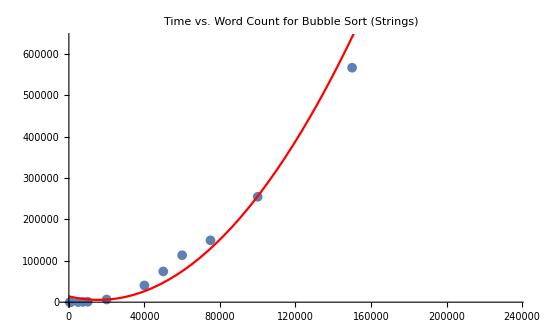

Set::write: Tag List in {499500, 49995000, 4999950000, 11249925000, 199990000, 27820984555, 799980000, 124750, 12497500, 1249975000, 1799970000, 28121250, 2812462500}[words_] is Protected.

-2.26477×10^9+106594. words

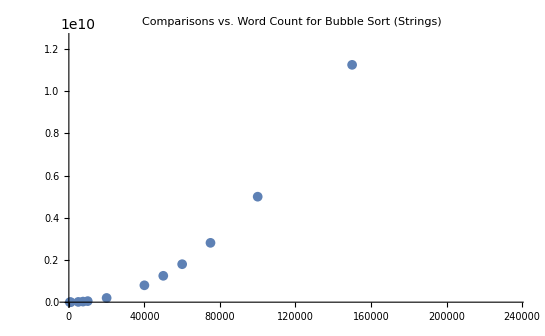

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Bubble Sort (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Bubble Sort (Strings)"]
```